```mathematica
ClearAll["Global`*"];
```

```mathematica
NotebookDirectory[];

(*list the possible subfolders (init files) that are present*)

fileList={
"init_1",
"init_2",
"init_3",
"init_4",
"init_5",
"init_6",
"init_7"
};
```

```mathematica
makestresstrain[folder_]:= {
(*PULLING AND COLLATING DATA FROM THE SIMULATIONS*)
(*imports data from the simulation outputs*)
inStretch = {};
inEnergy = {};
For[i = 1, i≤Length@fileList,i++,
AppendTo[inStretch, Import[#,"CSV"]&/@FileNames["StretchOut.dat",NotebookDirectory[]<>folder<>fileList⟦i⟧,Infinity]];
AppendTo[inEnergy, Import[#]&/@FileNames["EnergyOut.dat",NotebookDirectory[]<> folder<>fileList⟦i⟧,Infinity]];
];
(*isolates relevant data from the files*)
stretchTab = inStretch⟦;;,;;,1,2;;3⟧;
totEnergy = inEnergy[[;;,;;,3]];
(*puts all the data together into one list*)
energyTab = Table[Table[{stretchTab[[i,j,1]], stretchTab[[i,j,2]], i, totEnergy[[i, j, 1]]},{j, 1, Length@totEnergy[[i]]}], {i, 1, Length@totEnergy}];

(*isolates zero force runs*)
zeroForce = Table[energyTab[[i,1]],{i,1,Length@fileList}];
zeroForceSorted = SortBy[zeroForce, Last];
minx = zeroForceSorted[[1,1]];
miny = zeroForceSorted[[1,2]];

(*eliminates zero force runs from energyTab, gets the minimum energy runs*)
energyTabSans = Table[Table[{energyTab[[i,j,1]], energyTab[[i,j,2]],  energyTab[[i,j,3]],  energyTab[[i,j,4]]},{j,2, Length@energyTab[[i]]}], {i, 1, Length@energyTab}];
energyTabGathered = GatherBy[Flatten[energyTabSans,1],First];
energyTabSorted = Table[SortBy[energyTabGathered[[i]],Last], {i,1,Length@energyTabGathered}];
minEnergy = SortBy[energyTabSorted[[;;,1]],First];
(*min energy is xdim ydim init energy*)
plotEnergy = Table[{minEnergy[[i,1]], minEnergy[[i,4]]}, {i,1,Length@minEnergy}];


(*find discrete derivative to caclculate the force*)
forcex = {};
For[i=2,i<Length@minEnergy,i++, AppendTo[forcex, (minEnergy[[i+1,4]]-minEnergy[[i-1,4]])/(minEnergy[[i+1,1]]-minEnergy[[i-1,1]])]];

(*identifies if the midpoint of the discrete derivative is skewed, should be zero if not skewed*)
differences = Table[(minEnergy[[i+1,1]]- minEnergy[[i,1]])-(minEnergy[[i,1]]-minEnergy[[i-1,1]]), {i,2,Length@minEnergy-1}];

strainx = Table[(minEnergy[[i,1]]-minx)/minx,{i,2,Length@minEnergy}];

strainy = Table[(minEnergy[[i,2]]-miny)/miny, {i,2,Length@minEnergy}];

stressy = 0;

(*only records data when the midpoint of the discrete derivative isn't skewed*)
fordatx= Table[DeleteMissing[If[differences[[i]]<0.001, {forcex[[i]]/miny,stressy, strainx[[i]], strainy[[i]]}, Missing[]]], {i,1,Length@differences}];
stressstrain = Table[{fordatx[[i,3]],fordatx[[i,1]]},{i,1,Length@fordatx}]
}

makestresstrainy[folder_]:= {
(*imports data from the simulation outputs*)
inStretch = {};
inEnergy = {};
For[i = 1, i≤Length@fileList,i++,
AppendTo[inStretch, Import[#,"CSV"]&/@FileNames["StretchOut.dat",NotebookDirectory[]<>folder<>fileList⟦i⟧,Infinity]];
AppendTo[inEnergy, Import[#]&/@FileNames["EnergyOut.dat",NotebookDirectory[]<> folder<>fileList⟦i⟧,Infinity]];
];
(*isolates relevant data from the files*)
stretchTab = inStretch⟦;;,;;,1,2;;3⟧;
totEnergy = inEnergy[[;;,;;,3]];
(*HERE IS THE DIFFERENCE BETWEEN X,Y !!!!!!!!!!!!!!!!!!!*)
(*RIGHT HERE*)
(*puts all the data together into one list*)
energyTab = Table[Table[{stretchTab[[i,j,2]], stretchTab[[i,j,1]], i, totEnergy[[i, j, 1]]},{j, 1, Length@totEnergy[[i]]}], {i, 1, Length@totEnergy}];

(*isolates zero force runs*)
zeroForce = Table[energyTab[[i,1]],{i,1,Length@fileList}];
zeroForceSorted = SortBy[zeroForce, Last];
minx = zeroForceSorted[[1,2]];
miny = zeroForceSorted[[1,1]];


(*eliminates zero force runs from energyTab, gets the minimum energy runs*)
energyTabSans = Table[Table[{energyTab[[i,j,1]], energyTab[[i,j,2]],  energyTab[[i,j,3]],  energyTab[[i,j,4]]},{j,2, Length@energyTab[[i]]}], {i, 1, Length@energyTab}];
energyTabGathered = GatherBy[Flatten[energyTabSans,1],First];
energyTabSorted = Table[SortBy[energyTabGathered[[i]],Last], {i,1,Length@energyTabGathered}];
minEnergy = SortBy[energyTabSorted[[;;,1]],First];
(*min energy is ydim xdim init energy*)


(*find discrete derivative to caclculate the force*)
forcey = {};
For[i=2,i<Length@minEnergy,i++, AppendTo[forcey, (minEnergy[[i+1,4]]-minEnergy[[i-1,4]])/(minEnergy[[i+1,1]]-minEnergy[[i-1,1]])]];

(*identifies if the midpoint of the discrete derivative is skewed, should be zero if not skewed*)
differences = Table[(minEnergy[[i+1,1]]- minEnergy[[i,1]])-(minEnergy[[i,1]]-minEnergy[[i-1,1]]), {i,2,Length@minEnergy-1}];

strainx = Table[(minEnergy[[i,2]]-minx)/minx,{i,2,Length@minEnergy}];

strainy = Table[(minEnergy[[i,1]]-miny)/miny, {i,2,Length@minEnergy}];

stressx = 0;

(*only records data when the midpoint of the discrete derivative isn't skewed*)
fordatx= Table[DeleteMissing[If[differences[[i]]<0.001, {stressx, forcey[[i]]/minx, strainx[[i]], strainy[[i]]}, Missing[]]], {i,1,Length@differences}];
stressstrain = Table[{fordatx[[i,4]],fordatx[[i,2]]},{i,1,Length@fordatx}]
}

makedatfile[datx_,daty_ ]:= {
dat=Join[datx,daty];
SetDirectory[NotebookDirectory[]];
Export["stockinetteacrylic.dat", dat, "CSV"]
}

analyzedata[data1_, lin1_, lin2_,jamlin_]:={
(* data being analyzed, linear part lower limit, linear part upper limit, jamlin is the upper bound of the *)
data = data1;
data = Flatten[data,1];
AppendTo[data, {0,0}];
sorteddata = SortBy[data, 1];

linearpart = {};
For[i=1, i≤ Length@sorteddata, i++, If[lin1<sorteddata[[i,1]]<lin2,AppendTo[linearpart, {sorteddata[[i,1]], sorteddata[[i,2]]}]]];
linear = a + b*x;
linearfit=FindFit[linearpart,linear,{a,b},x];
linearyint = a/.linearfit[[1]];
linearslope = b/.linearfit[[2]];
plotlinearfit = Fit[linearpart, {1,x},x];
lf=NonlinearModelFit[linearpart,a x+b,{a,b},x];
lfdata=lf[{"BestFitParameters","ParameterTable", "ParameterErrors"}];
linearyint=Around[b/.lfdata[[1,2]],lfdata[[3,2]]];

jammedpart = {};
For[i=1, i≤ Length@sorteddata, i++, If[0<sorteddata[[i,1]]<jamlin,AppendTo[jammedpart, {sorteddata[[i,1]], sorteddata[[i,2]]}]]];
jamslope = sorteddata[[2,2]]/sorteddata[[2,1]];
jammedfit=FindFit[jammedpart,linear,{a,b},x];
jammedyint = a/.jammedfit[[1]];
jammedslope = b/.jammedfit[[2]];
jf=NonlinearModelFit[jammedpart,a x,{a},x];
jfdata=jf[{"BestFitParameters","ParameterTable", "ParameterErrors"}];
jammedslope=Around[a/.jfdata[[1]],jfdata[[3,1]]];
sloperatio = linearslope/jamslope;
anothersloperatio = jamslope/linearslope;
dataout = {sloperatio, anothersloperatio, jamslope, linearslope, linearyint, jammedslope, jammedyint, jammedslope/linearslope}
}

findenergyy[folder_, xmin_, ymin_]:= {
(*PULLING AND COLLATING DATA FROM THE SIMULATIONS*)
(*imports data from the simulation outputs*)
inStretch = {};
inEnergy = {};
For[i = 1, i≤Length@fileList,i++,
AppendTo[inStretch, Import[#,"CSV"]&/@FileNames["StretchOut.dat",NotebookDirectory[]<>folder<>fileList⟦i⟧,Infinity]];
AppendTo[inEnergy, Import[#]&/@FileNames["EnergyOut.dat",NotebookDirectory[]<> folder<>fileList⟦i⟧,Infinity]];
];
(*isolates relevant data from the files*)
stretchTab = inStretch⟦;;,;;,1,2;;3⟧;
totEnergy = inEnergy[[;;,;;,1;;3]];
(*puts all the data together into one list*)
energyTab = Table[Table[{stretchTab[[i,j,2]], stretchTab[[i,j,1]], i, totEnergy[[i, j, 1,1]], totEnergy[[i, j, 2,1]], totEnergy[[i, j, 3,1]]},{j, 1, Length@totEnergy[[i]]}], {i, 1, Length@totEnergy}];
(*y x init energy*)
energyTabGathered = GatherBy[Flatten[energyTab,1],First];
(* for given value of y, find min energy run*)
energyTabSorted = Table[SortBy[energyTabGathered[[i]], Last],{i, 1, Length@energyTabGathered}];
energyTabSorted = Table[DeleteMissing[Table[If[0.01< energyTabSorted[[i,j, 6]]<100,{energyTabSorted[[i,j,1]],energyTabSorted[[i,j,2]],energyTabSorted[[i,j,3]], energyTabSorted[[i,j, 4]],energyTabSorted[[i,j, 5]],energyTabSorted[[i,j, 6]]},Missing[]],{j, 1, Length@energyTabSorted[[i]]}]],{i,1,Length@energyTabSorted}];
fuckfuckfuck = {};
For[i=1,i≤Length@energyTabSorted, i++,If[Length@energyTabSorted[[i]]!=0,AppendTo[fuckfuckfuck, energyTabSorted[[i]]] ]];
minEnergy = SortBy[fuckfuckfuck[[;;,1]],First];
minEnergyall = SortBy[fuckfuckfuck[[;;,1]],First];
zeroforceruns=Table[minEnergyall[[i]],{i,1,4}];
zeroForcesim=SortBy[zeroforceruns,Last];
zeroForcesimzero= zeroForcesim[[1]];
minEnergy = Table[minEnergyall[[i]],{i,5,Length@minEnergyall}];
minEnergy=AppendTo[minEnergy, zeroForcesimzero];
minEnergy=SortBy[minEnergy,First];

xstrain = Table[(minEnergy[[i,2]]-xmin)/xmin, {i,1,Length@minEnergy}];
ystrain = Table[(minEnergy[[i,1]]-ymin)/ymin, {i,1,Length@minEnergy}];
plotcontact2d = Table[{ystrain[[i]], minEnergy[[i,4]]}, {i,1,Length@minEnergy}];
plotcontact3d = Table[{xstrain[[i]],ystrain[[i]], minEnergy[[i,4]]}, {i,1,Length@minEnergy}];
plotbend2d = Table[{ystrain[[i]], minEnergy[[i,5]]}, {i,1,Length@minEnergy}];
plotenergy2d = Table[{ystrain[[i]], minEnergy[[i,6]]}, {i,1,Length@minEnergy}];
plotbend3d = Table[{xstrain[[i]],ystrain[[i]], minEnergy[[i,5]]}, {i,1,Length@minEnergy}];
plotbend2dratio =Table[{ystrain[[i]], minEnergy[[i,5]](*/minEnergy[[i,6]]*)}, {i,1,Length@minEnergy}];
plotcontact2dratio = Table[{ystrain[[i]], minEnergy[[i,4]](*/minEnergy[[i,6]]*)}, {i,1,Length@minEnergy}];
contactratio = Table[minEnergy[[i,4]](*/minEnergy[[i,6]]*), {i,1,Length@minEnergy}];
bendratio = Table[minEnergy[[i,5]](*/minEnergy[[i,6]]*), {i,1,Length@minEnergy}];
energymap = Table[{xstrain[[i]], ystrain[[i]], minEnergy[[i,6]]}, {i,1,Length@minEnergy}]
}

findenergyx[folder_, xmin_, ymin_]:= {
(*PULLING AND COLLATING DATA FROM THE SIMULATIONS*)
(*imports data from the simulation outputs*)
inStretch = {};
inEnergy = {};
For[i = 1, i≤Length@fileList,i++,
AppendTo[inStretch, Import[#,"CSV"]&/@FileNames["StretchOut.dat",NotebookDirectory[]<>folder<>fileList⟦i⟧,Infinity]];
AppendTo[inEnergy, Import[#]&/@FileNames["EnergyOut.dat",NotebookDirectory[]<> folder<>fileList⟦i⟧,Infinity]];
];
(*isolates relevant data from the files*)
stretchTab = inStretch⟦;;,;;,1,2;;3⟧;
totEnergy = inEnergy[[;;,;;,1;;3]];
(*puts all the data together into one list*)
energyTab = Table[Table[{stretchTab[[i,j,1]], stretchTab[[i,j,2]], i, totEnergy[[i, j, 1,1]], totEnergy[[i, j, 2,1]], totEnergy[[i, j, 3,1]]},{j, 1, Length@totEnergy[[i]]}], {i, 1, Length@totEnergy}];
(* x y init energy*)
energyTabGathered = GatherBy[Flatten[energyTab,1],First];
(* for given value of y, find min energy run*)
energyTabSorted = Table[SortBy[energyTabGathered[[i]], Last],{i, 1, Length@energyTabGathered}];
energyTabSorted = Table[DeleteMissing[Table[If[0.01< energyTabSorted[[i,j, 6]]<100,{energyTabSorted[[i,j,1]],energyTabSorted[[i,j,2]],energyTabSorted[[i,j,3]], energyTabSorted[[i,j, 4]],energyTabSorted[[i,j, 5]],energyTabSorted[[i,j, 6]]},Missing[]],{j, 1, Length@energyTabSorted[[i]]}]],{i,1,Length@energyTabSorted}];
fuckfuckfuck = {};
For[i=1,i≤Length@energyTabSorted, i++,If[Length@energyTabSorted[[i]]!=0,AppendTo[fuckfuckfuck, energyTabSorted[[i]]] ]];
minEnergyall = SortBy[fuckfuckfuck[[;;,1]],First];
zeroforceruns=Table[minEnergyall[[i]],{i,1,4}];
zeroForcesim=SortBy[zeroforceruns,Last];
zeroForcesimzero= zeroForcesim[[1]];
minEnergy = Table[minEnergyall[[i]],{i,5,Length@minEnergyall}];
minEnergy=AppendTo[minEnergy, zeroForcesimzero];
minEnergy=SortBy[minEnergy,First];

xstrain = Table[(minEnergy[[i,1]]-xmin)/xmin, {i,1,Length@minEnergy}];
ystrain = Table[(minEnergy[[i,2]]-ymin)/ymin, {i,1,Length@minEnergy}];
plotcontact2d = Table[{xstrain[[i]], minEnergy[[i,4]]}, {i,1,Length@minEnergy}];
plotcontact3d = Table[{xstrain[[i]],ystrain[[i]], minEnergy[[i,4]]}, {i,1,Length@minEnergy}];
plotbend2d = Table[{ystrain[[i]], minEnergy[[i,5]]}, {i,1,Length@minEnergy}];
plotenergy2d = Table[{xstrain[[i]], minEnergy[[i,6]]}, {i,1,Length@minEnergy}];
plotbend3d = Table[{xstrain[[i]],ystrain[[i]], minEnergy[[i,5]]}, {i,1,Length@minEnergy}];
plotbend2dratio =Table[{xstrain[[i]], minEnergy[[i,5]](*/minEnergy[[i,6]]*)}, {i,1,Length@minEnergy}];
plotcontact2dratio = Table[{xstrain[[i]], minEnergy[[i,4]]}, {i,1,Length@minEnergy}];
contactratio = Table[minEnergy[[i,4]], {i,1,Length@minEnergy}];
bendratio = Table[minEnergy[[i,5]], {i,1,Length@minEnergy}];
energymap = Table[{xstrain[[i]], ystrain[[i]], minEnergy[[i,6]]}, {i,1,Length@minEnergy}]
}
```

```mathematica
yintlist1 = {};
jammedslopelist1 = {};
energyratiolist1 = {};
energyratiolist1bend = {};
```

Part::partw: Part 1 of {} does not exist.

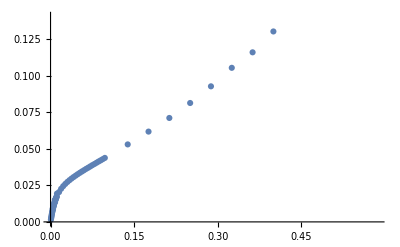

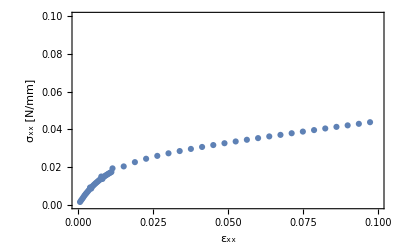

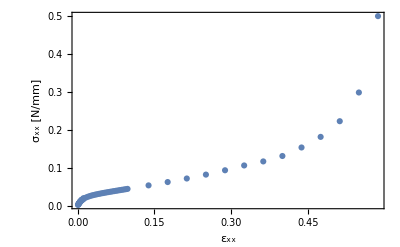

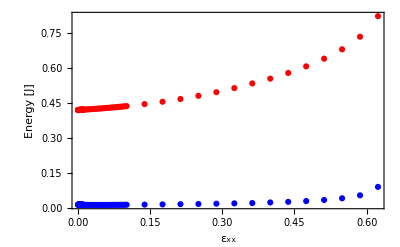

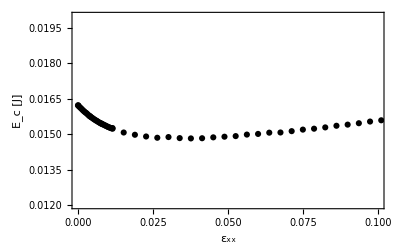

-Graphics-

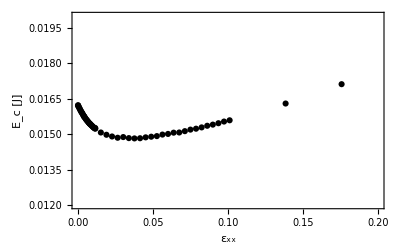

```mathematica
sim="k1len10500x/";
data = makestresstrain[sim];
len = 10.0; (*the thing I am changing with this simulation*)

ListPlot[data]
Show[ListPlot[data, PlotRange->{{0,0.1},{0,0.1}},Frame->True, FrameLabel->{"ε_xx","σ_xx [N/mm]"}, FrameStyle->Directive[Black,FontFamily->"Helvetica",Thickness[0.005],Arrowheads[{0.0,0.05}], 15], PlotRangePadding-> None]]
Show[ListPlot[data, PlotRange->All,Frame->True, FrameLabel->{"ε_xx","σ_xx [N/mm]"}, FrameStyle->Directive[Black,FontFamily->"Helvetica",Thickness[0.005],Arrowheads[{0.0,0.05}], 15], PlotRangePadding-> None]]
analyzedata[data, 0.05,0.1,0.02];
AppendTo[yintlist1, {len, linearyint}];
AppendTo[jammedslopelist1, {len,jammedslope}];
minx;
miny;

findenergyx[sim, minx, miny];
energyplot =Show[ListPlot[plotbend2dratio, PlotStyle->Red, PlotLegends->Placed[{Style["Bending Energy", FontSize->10, FontFamily->"Helvetica"]}, {Left,Center}]],
 ListPlot[plotcontact2dratio, PlotStyle-> Blue, PlotLegends->Placed[{Style["Compression Energy", FontSize->10, FontFamily->"Helvetica"]},{Left,Center}]],
PlotRange->All, Frame->True, FrameLabel->{"ε_xx","Energy [J]"}, FrameStyle->Directive[Black,FontFamily->"Helvetica",Thickness[0.005],Arrowheads[{0.0,0.05}], 10], PlotRangePadding-> None]

energyplot =Show[(*ListPlot[plotbend2dratio, PlotStyle->Red, PlotLegends->Placed[{Style["Bending Energy", FontSize->10, FontFamily->"Helvetica"]}, {Left,Center}]],*)
 ListPlot[plotcontact2dratio, PlotStyle-> Black(*, PlotLegends->Placed[{Style["Compression Energy", FontSize->10, FontFamily->"Helvetica"]},{Left,Center}]*),PlotRange->{{0,0.2},{0.012,0.02}}],
PlotRange->{{0,0.1},{0.012,0.02}}, Frame->True, FrameLabel->{"ε_xx","E_c [J]"}, FrameStyle->Directive[Black,FontFamily->"Helvetica",Thickness[0.005],Arrowheads[{0.0,0.05}], 15], PlotRangePadding-> None]

mincontact = Min[contactratio];
minEnergyall;
energydiff = contactratio[[1]] - mincontact;
AppendTo[energyratiolist1, {len, energydiff}];

minbend = Min[bendratio];
minEnergy;
energydiff = bendratio[[1]] - minbend;
AppendTo[energyratiolist1bend, {len, energydiff}];
```

```mathematica
ffs=Show[-Graphics-]
ffsenergy=Show[-Graphics-]
SetDirectory[NotebookDirectory[]];
Export["jammedwinset.pdf",ffs]
Export["jammedcontactenergy.pdf",ffsenergy]
```

-Graphics-

-Graphics-

jammedwinset.pdf

jammedcontactenergy.pdf

```mathematica
(* process more simulations in the x-direction and then you can see how things change with the variable that is changing*)
```

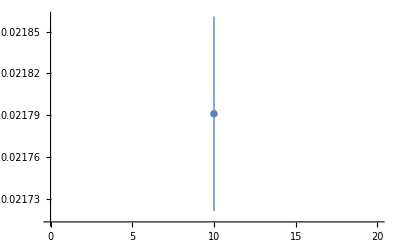

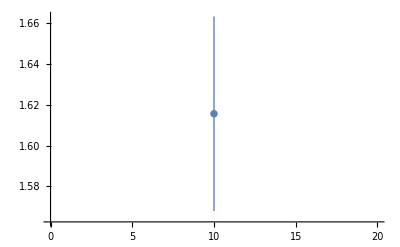

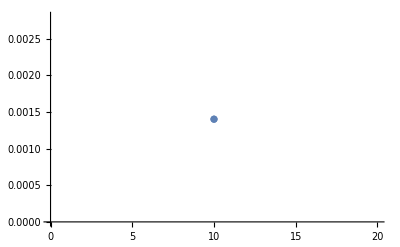

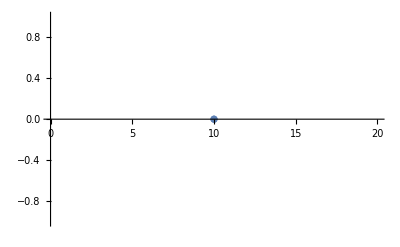

```mathematica
ListPlot[yintlist1]
ListPlot[jammedslopelist1]
ListPlot[energyratiolist1]
ListPlot[energyratiolist1bend]
```

```mathematica
yintlist1y = {};
jammedslopelist1y = {};
energyratiolist1y = {};
energyratiolist1bendy = {};
```

Part::partw: Part 1 of {} does not exist.

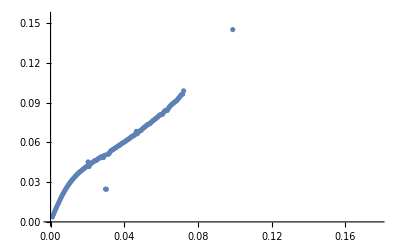

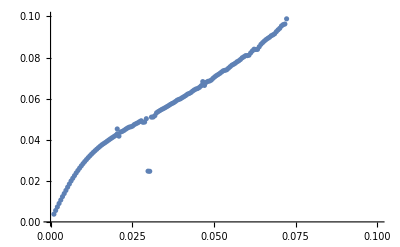

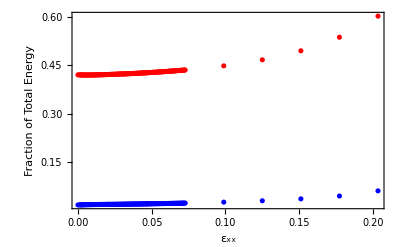

```mathematica
sim="k1len10500y/";
data = makestresstrainy[sim];
len = 10.0; (*the thing I am changing with this simulation*)

ListPlot[data]
ListPlot[data, PlotRange->{{0,0.1},{0,0.1}}]
analyzedata[data, 0.05,0.1,0.02];
AppendTo[yintlist1y, {len, linearyint}];
AppendTo[jammedslopelist1y, {len,jammedslope}];
minx;
miny;

findenergyy[sim, minx, miny];
energyplot =Show[ListPlot[plotbend2dratio, PlotStyle->Red, PlotLegends->Placed[{Style["Bending Energy", FontSize->10, FontFamily->"Helvetica"]}, {Left,Center}]],
 ListPlot[plotcontact2dratio, PlotStyle-> Blue, PlotLegends->Placed[{Style["Compression Energy", FontSize->10, FontFamily->"Helvetica"]},{Left,Center}]],
PlotRange->All, Frame->True, FrameLabel->{"ε_xx","Fraction of Total Energy"}, FrameStyle->Directive[Black,FontFamily->"Helvetica",Thickness[0.005],Arrowheads[{0.0,0.05}], 10], PlotRangePadding-> None]

mincontact = Min[contactratio];
minEnergyall;
energydiff = contactratio[[1]] - mincontact;
AppendTo[energyratiolist1y, {len, energydiff}];

minbend = Min[bendratio];
minEnergy;
energydiff = bendratio[[1]] - minbend;
AppendTo[energyratiolist1bendy, {len, energydiff}];
```

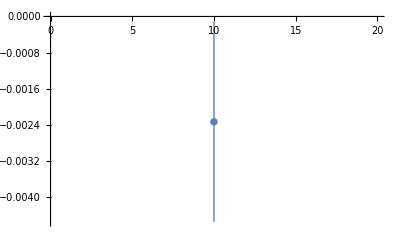

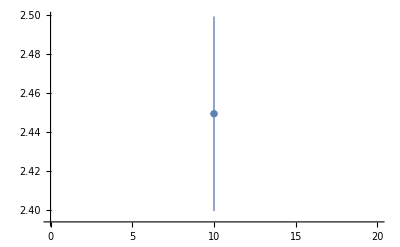

-Graphics-

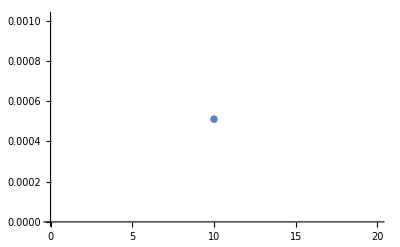

```mathematica
ListPlot[yintlist1y]
ListPlot[jammedslopelist1y]
ListPlot[energyratiolist1y]
ListPlot[energyratiolist1bendy]
```